```mathematica
(*Soluciones al sistema para algunas condiciones iniciales determinadas y diagrama del logaritmo de la diferencia de las trayectorias*)
```

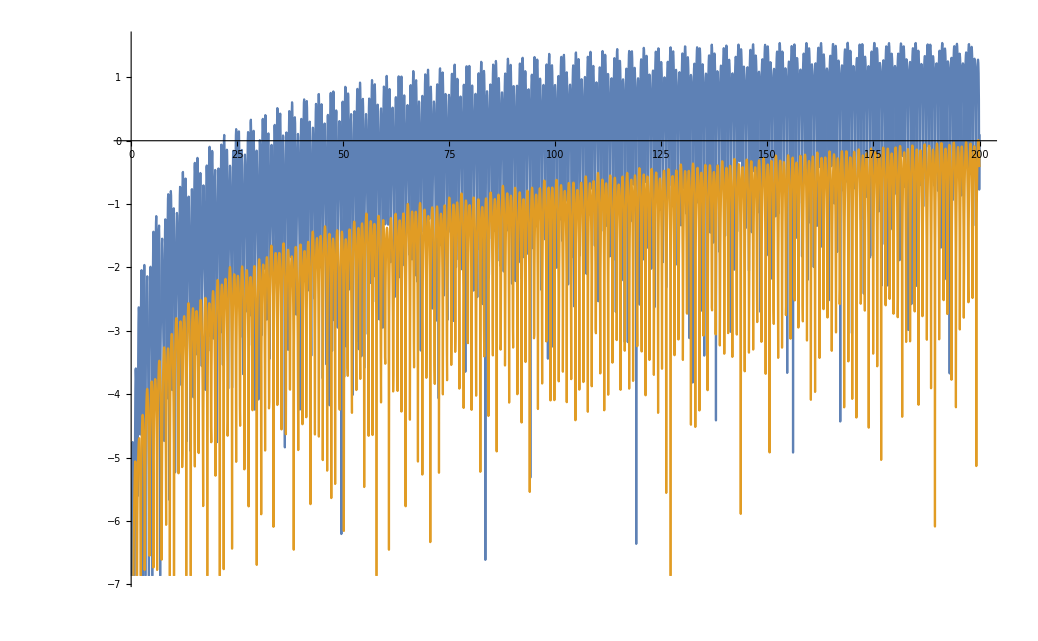

```mathematica
mu = 0.5;
abc={x'[t]== z[t] + 0.5*z[t]*(z[t]^2 + x[t]^2),y'[t]== w[t] + 0.5*w[t]*(w[t]^2 + y[t]^2), z'[t]== -x[t]*(1 + 2*mu*y[t]^2 +  0.5*(z[t]^2 + x[t]^2)),w'[t]==-y[t]*(1 + 2*mu*x[t]^2 + 0.5*(w[t]^2 + y[t]^2))};
psect[{x0_,y0_,z0_,w0_}]:=NDSolve[{abc,x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0},{x[t],y[t],z[t],w[t]},{t,0,1000},MaxSteps->Infinity];
s = psect[{2.207,0.382,-0.748,-2.492}];
s2 = psect[{2.207,0.382,-0.748,-2.502}];
s3 = psect[{-0.749,-0.196,-1.926,0.941}];
s4 = psect[{-0.749,-0.196,-1.926,0.951}];

H [x_,y_,z_,w_]:= 1/2 (z^2+w^2)+ 1/2 (x^2+y^2) + 1/8(z^2+x^2)^2 + 1/8(w^2+y^2)^2  + mu*(x^2)*(y^2);
Plot[{Log[Abs[Evaluate[x[t]/.s] - Evaluate[x[t]/.s2]]],Log[Abs[Evaluate[x[t]/.s3] - Evaluate[x[t]/.s4]]]}, {t,0,200}]
```

```mathematica
mu = 0.5;
abc={x'[t]== z[t] + 0.5*z[t]*(z[t]^2 + x[t]^2),y'[t]== w[t] + 0.5*w[t]*(w[t]^2 + y[t]^2), z'[t]== -x[t]*(1 + 2*mu*y[t]^2 +  0.5*(z[t]^2 + x[t]^2)),w'[t]==-y[t]*(1 + 2*mu*x[t]^2 + 0.5*(w[t]^2 + y[t]^2))};
psect[{x0_,y0_,z0_,w0_}]:=NDSolve[{abc,x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0},{x[t],y[t],z[t],w[t]},{t,0,100},MaxSteps->Infinity];
s = psect[{-0.749,-0.196,-1.926,0.941}];
s2 = psect[{-0.749,-0.196,-1.926,0.951}];
H [x_,y_,z_,w_]:= 1/2 (z^2+w^2)+ 1/2 (x^2+y^2) + 1/8(z^2+x^2)^2 + 1/8(w^2+y^2)^2  + mu*(x^2)*(y^2);
Plot[Log[Abs[Evaluate[x[t]/.s] - Evaluate[x[t]/.s2]]], {t,0,100}]
```

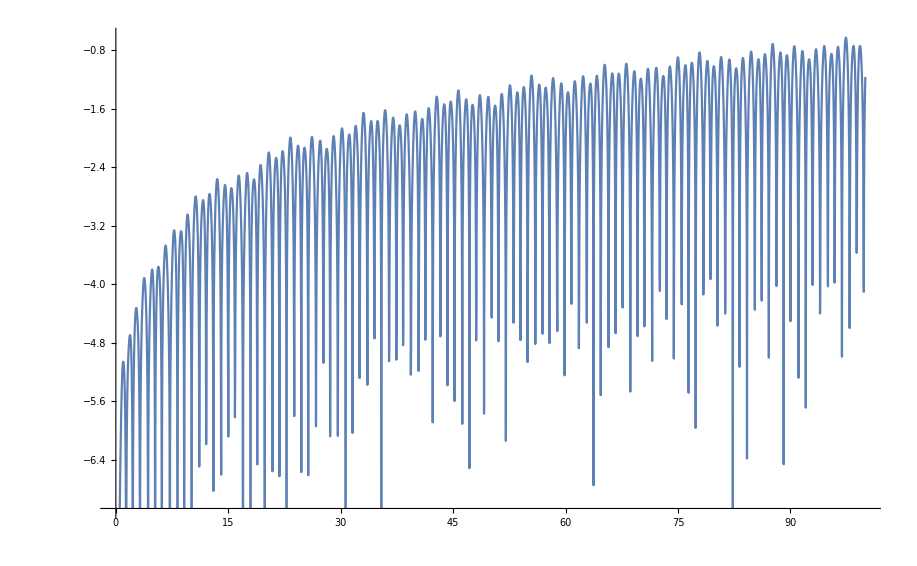
```mathematica
-Graphics-
(*Gráfica de las cantidades conservadas del sistema*)
```

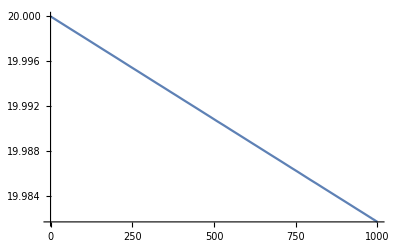

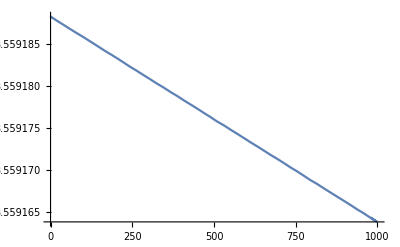

```mathematica
mu = 0.0;
abc={x'[t]== z[t] + 0.5*z[t]*(z[t]^2 + x[t]^2),y'[t]== w[t] + 0.5*w[t]*(w[t]^2 + y[t]^2), z'[t]== -x[t]*(1 + 2*mu*y[t]^2 +  0.5*(z[t]^2 + x[t]^2)),w'[t]==-y[t]*(1 + 2*mu*x[t]^2 + 0.5*(w[t]^2 + y[t]^2))};
psect[{x0_,y0_,z0_,w0_}]:=NDSolve[{abc,x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0},{x[t],y[t],z[t],w[t]},{t,0,1000},MaxSteps->Infinity];
s = psect[{-1.8150888896235369,-1.243306249002618,-0.5144322959884681,-2.8570903314769964}];

H [x_,y_,z_,w_]:= 1/2 (z^2+w^2)+ 1/2 (x^2+y^2) + 1/8(z^2+x^2)^2 + 1/8(w^2+y^2)^2  + mu*(x^2)*(y^2);
F[x_, z_] := z^2 + x^2
F2[y_, w_] := y^2 + w^2
Plot[H[Evaluate[x[t]/.s],Evaluate[y[t]/.s], Evaluate[z[t]/.s] , Evaluate[w[t]/.s]], {t,0,1000}]
Plot[F[Evaluate[x[t]/.s] , Evaluate[z[t]/.s]], {t,0,1000}]
```